```mathematica
SetDirectory[NotebookDirectory[]];Get["RunCoinStackingCode.m",Path->{PersistentSymbol["persistentGitHubPath","Local"]}]
Get["CoinStackingCode.m",Path->{PersistentSymbol["persistentGitHubPath","Local"]}]
Get["LatticePhyllotaxis.m",Path->{PersistentSymbol["persistentGitHubPath","Local"]}];
```

```mathematica
runParameters= <|"rScale"->6,"rSlope"->0.03,"zMax"->15,"runNumber"->1,"diskMax"->∞|>;
run = makeRunFromParameter[runParameters];
res=executeRun[run];
```

Print some lopsided nodes

run complete

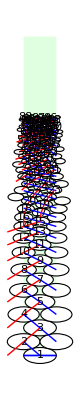

```mathematica
showRun[res]
```

```mathematica
{etiming,experimentTest} = Timing@runParameterSets[ Take[makeExperimentParameters[{10}, Subdivide[0.03 ,0.06,2],{22}],All]];etiming
```

57.9688

```mathematica
cylinderLU = If[MissingQ[run["Arena"]["CylinderLU"]],{0,20},run["Arena"]["CylinderLU"]]
```

{0,20}

```mathematica
(* for display, not for calculation  *) 

diskAndVisibleCopies[Disk[{x_,z_},r_]] := {Disk[{x,z},r],If[x+r>1/2,moveDiskLeft[Disk[{x,z},r]],Nothing[]],If[x-r<-1/2,moveDiskRight[Disk[{x,z},r]],Nothing[]]};

showDiskXZ[run_,n_] := run["DiskData"][n]["Disk"];

showRun[run_] := Module[{disks,chains,ffs,cylinder,contacts},
ffs= Directive[FaceForm[White],EdgeForm[Black]];
disks =Association@Map[#->showDiskXZ[run,#]&,
Select[VertexList[run["ContactGraph"]],bareNumberQ]];

contacts = graphToContactLines[run];

cylinderLU = If[MissingQ[run["Arena"]["CylinderLU"]],{0,20},run["Arena"]["CylinderLU"]];
cylinder = {LightGreen,Rectangle[{-1/2,cylinderLU[[1]]},{1/2,cylinderLU[[2]]}]};

Graphics[{
cylinder
,{ffs,Map[diskAndVisibleCopies,Values@disks]}

(*,{Black,chains}
*)
,{contacts}
,KeyValueMap[Text[#1,#2[[1]]]&,disks]
}
,Axes->False
]
];

graphToContactLines[run_] := Module[{g,dlines,res},
g = run["ContactGraph"];
dlines = Line/@Map[diskXZ[getDiskFromRun[run,#]]&,List@@@EdgeList[g],{2}];
res = lineCylinderIntersectionColoured/@dlines;
res
];
lineCylinderIntersectionColoured[Line[{{x1_,z1_},{x2_,z2_}}]] := Module[{slope,col},
slope= (z2-z1)/(x2-x1);
If[slope>0,col=Red,col=Blue];
If[x1<-1/2,
Return[{col,Line[{{-1/2, z2 - slope * (x2-(-1/2))},{x2,z2}}]
, Line[{{x1+1,z1},{1/2,z1+slope *( 1/2-(1+x1))}}]
}]];
If[x2>1/2,
Return[{col,Line[{{-1/2, z2- slope * (x2-1-(-1/2))},{x2-1,z2}}]
, Line[{{x1,z1},{1/2,z1+slope *( 1/2-(x1))}}]
}]];
Return[{col,Line[{{x1,z1},{x2,z2}}]}] 
];
```